Let’s look at how the quasi-uniform mode’s dispersion is affected by DMI.
The analytic expression by Moon et al will be put on top of the data.

DMI on TOP only!
Single material (NiFe).

## The Eigenfrequencies

#### Some parameters needed for the code

```mathematica
B=0.03;
Δ=1;
Φ[0]=Table[0,{4}];
```

```mathematica
LL=4;
```

```mathematica
a=0.248 10^-9;  (*0.25 nm atomic spacing*)
Ms=835563; (*A/m*)
AA=1.355 10^-11;  (*J/m*)
DD =4.2 10^-3 1/1; (* i.e. This is 4.2 mJ/m^2 for 1 layer and decreases for thicker films!*)
JJ=(2 AA)/(a^2 Ms)
```

527.335

```mathematica
K[i_]:=K[i]=Which[i<LL/2+0.5,0,i>LL/2+0.5,0]
J[i_]:=J[i]=Which[i<LL/2+0.5,JJ,i>LL/2+0.5,JJ]
H[i_]:=H[i]=Which[i<LL/2+0.5,B,i>LL/2+0.5,B]
HDMI[1]=2 DD/(a Ms);
HDMI[4]=0
```

0

```mathematica
ϕ[i_]:=ϕ[i]=0
```

#### Coding required to create dynamical matrix

For a typical plane of spins in the wall the code is:

```mathematica
acomponent[i_,y_,z_]:=acomponent[i,y,z]=H[i] Cos[ϕ[i]]+(4 π 10^-7) Ms+2 K[i] (Cos[ϕ[i]]^2-Sin[ϕ[i]]^2)+J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])+4 J[i]-2 J[i] Cos[y]-2 J[i] Cos[z]
aplus[i_]:=aplus[i]=-J[i] Cos[ϕ[i]-ϕ[i+1]]
aminus[i_]:=aminus[i]=-J[i] Cos[ϕ[i]-ϕ[i-1]]
bcomponent[i_,y_,z_]:=bcomponent[i,y,z]=-H[i] Cos[ϕ[i]]-2 K[i] Cos[ϕ[i]]^2-J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])-4 J[i]+2 J[i] Cos[y]+2 J[i] Cos[z]
```

```mathematica
rowa[NN_,k_,y_,z_]:=Join[Table[0,{2 k-3}],{aminus[k],0,acomponent[k,y,z],0,aplus[k]},Table[0,{2 NN-2-2 k}]]
rowb[NN_,k_,y_,z_]:=Join[Table[0,{2 k-4}],{J[k],0,bcomponent[k,y,z],0,J[k]},Table[0,{2 NN-1-2 k}]]
```

The 1st, (N/2)th, (N/2 +1)th and Nth planes all need individual codes sinse they have different exchange coupling to the planes on either side.
The codes are as follows:

```mathematica
arow1[NN_,y_,z_]:=arow1[NN,y,z]=Join[
{-HDMI[1] Sin[y] ⅈ,
H[1] Cos[ϕ[1]]+(4 π 10^-7) Ms+2 K[1] (Cos[ϕ[1]]^2-Sin[ϕ[1]]^2)+J[1] (0+Cos[ϕ[1]-ϕ[2]])+4 J[1]-2 J[1] Cos[y]-2 J[1] Cos[z],
0,
aplus[1]},
Table[0,{2 NN-4}]];
```

```mathematica
brow1[NN_,y_,z_]:=brow1[NN,y,z]=Join[
{-H[1] Cos[ϕ[1]]-2 K[1] Cos[ϕ[1]]^2-J[1] (0+Cos[ϕ[1]-ϕ[2]])-4 J[1]+2 J[1] Cos[y]+2 J[1] Cos[z],
-HDMI[1] Sin[y] ⅈ,
J[2]},
Table[0,{2 NN-3}]];
```

Note that I have kept the ANGULAR dependence in this code, which was set up for dealing with an exchange spring. It is not needed here, but it is an interesting question to see how the DMI can change the modes on an exchange spring...

```mathematica
arow50[NN_,y_,z_,β_]:=arow50[NN,y,z,β]=Join[
Table[0,{NN -3}],
{aminus[NN/2],
0,
H[NN/2] Cos[ϕ[NN/2]]+(4 π 10^-7) Ms+2 K[NN/2] (Cos[ϕ[NN/2]]^2-Sin[ϕ[NN/2]]^2)+J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2]]+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]+4 J[NN/2]-2 J[NN/2] Cos[y]-2 J[NN/2] Cos[z],
0,
-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]},
Table[0,{NN-2}]]
```

```mathematica
brow50[NN_,y_,z_,β_]:=brow50[NN,y,z,β]=Join[
Table[0,{NN-4}],
{J[NN/2],
0,
-H[NN/2] Cos[ϕ[NN/2]]-2 K[NN/2] Cos[ϕ[NN/2]]^2-J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2-1]]-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]-4 J[NN/2]+2 J[NN/2] Cos[y]+2 J[NN/2] Cos[z],
0,
J[NN]+β (J[1]-J[NN])},
Table[0,{NN-1}]]
```

```mathematica
arow51[NN_,y_,z_,β_]:=arow51[NN,y,z,β]=Join[
Table[0,{NN-1}],
{-(J[NN/2]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]],
0,
H[NN/2+1] Cos[ϕ[NN/2+1]]+(4 π 10^-7) Ms+2 K[NN/2+1] (Cos[ϕ[NN/2+1]]^2-Sin[ϕ[NN/2+1]]^2)+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]+J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]+4 J[NN/2+1]-2 J[NN/2+1] Cos[y]-2 J[NN/2+1] Cos[z],
0,
aplus[NN/2+1]},
Table[0,{NN-4}]]
```

```mathematica
brow51[NN_,y_,z_,β_]:=brow51[NN,y,z,β]=Join[
Table[0,{NN-2}],
{J[NN]+β (J[1]-J[NN]),
0,
-H[NN/2+1] Cos[ϕ[NN/2+1]]-2 K[NN/2+1] Cos[ϕ[NN/2+1]]^2-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]-J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]-4 J[NN/2+1]+2 J[NN/2+1] Cos[y]+2 J[NN/2+1] Cos[z],
0,
J[NN/2+1]},
Table[0,{NN-3}]]
```

```mathematica
arow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-3}],
{aminus[NN],
-HDMI[NN] Sin[y] ⅈ,
H[NN] Cos[ϕ[NN]]+(4 π 10^-7) Ms+2 K[NN] (Cos[ϕ[NN]]^2-Sin[ϕ[NN]]^2)+J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)+4 J[NN]-2 J[NN] Cos[y]-2 J[NN] Cos[z]}];
```

```mathematica
brow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-4}],
{J[NN-1],
0,
-H[NN] Cos[ϕ[NN]]-2 K[NN] Cos[ϕ[NN]]^2-J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)-4 J[NN]+2 J[NN] Cos[y]+2 J[NN] Cos[z],
-HDMI[NN] Sin[y] ⅈ}];
```

#### The dynamical matrix and eigenfrequencies

The dynamical matrix is:

```mathematica
big[NN_,y_,z_,β_]:=big[NN,y,z,β]=Join[
{arow1[NN,y,z],brow1[NN,y,z]},
Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,2,NN/2-1}],1],{arow50[NN,y,z,β],brow50[NN,y,z,β],arow51[NN,y,z,β],brow51[NN,y,z,β]},Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,NN/2+2,NN-1}],1],
{arow100[NN,y,z],brow100[NN,y,z]}]
```

```mathematica
Eigenvalues[big[4,0.1,0,0.5]]
```

{-5.68434×10^-14-1806.56 ⅈ,2.27374×10^-13+1805.96 ⅈ,5.70391×10^-14-1061.51 ⅈ,4.57801×10^-13+1059.49 ⅈ,1.3211×10^-14-316.459 ⅈ,-2.40424×10^-17+313.005 ⅈ,1.00582×10^-14-6.80518 ⅈ,8.88174×10^-15+4.78167 ⅈ}

The eigenfrequencies are given by (γ = 176 GHz rad/T):

```mathematica
freqs[NN_,y_,z_,β_]:=freqs[NN,y,z,β]=176/(2. π)Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,2}]
```

```mathematica
freqs2[NN_,y_,z_,β_]:=freqs2[NN,y,z,β]=176/(2. π) Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,1}]
```

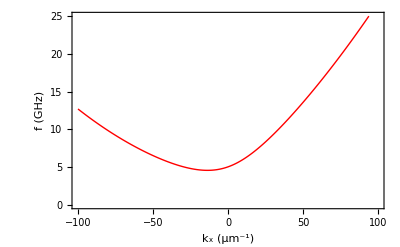

```mathematica
ListPlot[Table[{ky/10^6,If[freqs2[4,ky a,0,0.5][[1]]>0,freqs2[4,ky a,0,0.5][[1]],freqs2[4,ky a,0,0.5][[2]]] },{ky,-100 10^6,100 10^6,1 10^6}],Frame->True,FrameLabel->{"k_x (μm^-1)","f (GHz)"},PlotRange->{0,25},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->Directive[Red,Thick],FrameStyle->Directive[Black,Thick]]
```

```mathematica
withDMI={{-100,12.704878253588868},{-99,12.549679859861902},{-98,12.395814815648043},{-97,12.24327914721948},{-96,12.092068934656018},{-95,11.942180317836938},{-94,11.793609502895011},{-93,11.64635276889349},{-92,11.50040647511958},{-91,11.355767068580942},{-90,11.212431092180948},{-89,11.070395193239914},{-88,10.929656132502656},{-87,10.79021079390226},{-86,10.652056194614001},{-85,10.515189496049004},{-84,10.379608015154519},{-83,10.245309236755567},{-82,10.112290826371847},{-81,9.98055064399792},{-80,9.850086758600419},{-79,9.720897463624857},{-78,9.59298129337003},{-77,9.466337040370984},{-76,9.340963773924},{-75,9.216860859732149},{-74,9.094027980707757},{-73,8.972465159181798},{-72,8.852172780434652},{-71,8.733151617723149},{-70,8.615402858873798},{-69,8.498928134559046},{-68,8.383729548394976},{-67,8.269809708849046},{-66,8.157171763290748},{-65,8.045819434158895},{-64,7.935757057390806},{-63,7.826989623402514},{-62,7.719522820588895},{-61,7.613363081654602},{-60,7.508517632867335},{-59,7.404994546565838},{-58,7.302802796818844},{-57,7.20195231882442},{-56,7.102454071908027},{-55,7.004320106719225},{-54,6.907563636332647},{-53,6.812199112169584},{-52,6.718242304284643},{-51,6.625710386836316},{-50,6.534622028586616},{-49,6.444997488950504},{-48,6.356858719580604},{-47,6.2702294720397},{-46,6.185135411307907},{-45,6.101604235767747},{-44,6.019665803482027},{-43,5.939352265046507},{-42,5.86069820289722},{-41,5.783740777131579},{-40,5.708519877735167},{-39,5.635078282696119},{-38,5.5634618220336005},{-37,5.493719546673753},{-36,5.4259039017653246},{-35,5.360070903083551},{-34,5.296280315511819},{-33,5.234595831608407},{-32,5.175085248350408},{-31,5.117820639563471},{-30,5.062878520884082},{-29,5.010340003689603},{-28,4.960290934003544},{-27,4.912822010917046},{-26,4.868028879425384},{-25,4.82601219111913},{-24,4.78687762525819},{-23,4.750735862653864},{-22,4.7177025035397575},{-21,4.687897920204295},{-20,4.661447034734035},{-19,4.638479011921789},{-18,4.619126857895889},{-17,4.6035269148535765},{-16,4.591818244086933},{-15,4.58414189075401},{-14,4.580640025873519},{-13,4.581454964951905},{-12,4.586728065298865},{-11,4.596598509346653},{-10,4.611201985986214},{-9,4.6306692878008935},{-8,4.655124847150824},{-7,4.684685240110783},{-6,4.719457692327537},{-5,4.759538624229568},{-4,4.805012276526547},{-3,4.855949457266307},{-2,4.912406450868137},{-1,4.974424125908307},{0,5.042027273532291},{1,5.115224200524187},{2,5.194006591574462},{3,5.278349647012182},{4,5.368212489735653},{5,5.463538826800133},{6,5.564257841632358},{7,5.670285284997212},{8,5.781524727940789},{9,5.897868936290881},{10,6.019201325447296},{11,6.1453974545244625},{12,6.2763265224136395},{13,6.411852831698451},{14,6.5518371914212405},{15,6.696138235746905},{16,6.844613640643603},{17,6.99712122656725},{18,7.153519939834387},{19,7.313670710627577},{20,7.477437188224208},{21,7.644686357970584},{22,7.815289046548551},{23,7.98912032334621},{24,8.166059807549809},{25,8.345991890400411},{26,8.528805882561423},{27,8.71439609624764},{28,8.9026618713432},{29,9.093507554327552},{30,9.286842437584303},{31,9.482580666564685},{32,9.680641121366111},{33,9.880947277826866},{34,10.083427053596123},{35,10.288012643171554},{36,10.494640345469724},{37,10.703250387082093},{38,10.913786743708283},{39,11.1261969616744},{40,11.34043198152922},{41,11.556445964728459},{42,11.77419612475893},{43,11.99364256310997},{44,12.214748111159151},{45,12.43747817794539},{46,12.661800604347967},{47,12.887685523779092},{48,13.115105229331254},{49,13.344034047499422},{50,13.574448218195903},{51,13.806325781243173},{52,14.03964646870142},{53,14.274391603283744},{54,14.51054400230685},{55,14.748087887191325},{56,14.987008797991127},{57,15.22729351310685},{58,15.468929973364222},{59,15.711907210913054},{60,15.956215282030634},{61,16.20184520412356},{62,16.448788896328495},{63,16.6970391238531},{64,16.946589445468195},{65,17.19743416425437},{66,17.44956828127106},{67,17.702987452056476},{68,17.95768794564736},{69,18.213666606149793},{70,18.47092081657192},{71,18.729448464773316},{72,18.989247911557214},{73,19.25031796057279},{74,19.51265783003897},{75,19.77626712615113},{76,20.041145818054108},{77,20.307294214311415},{78,20.574712940695832},{79,20.843402919387024},{80,21.113365349325854},{81,21.384601687689518},{82,21.65711363250853},{83,21.930903106292252},{84,22.20597224052226},{85,22.482323361154968},{86,22.75995897484152},{87,23.03888175611082},{88,23.319094535028054},{89,23.600600285894178},{90,23.88340211625241},{91,24.167503256834355},{92,24.452907051796004},{93,24.739616949710513},{94,25.02763649504661},{95,25.316969319993692},{96,25.607619136965027},{97,25.899589731304474},{98,26.192884954609372},{99,26.48750871827662},{100,26.783464987510786}};
```

The following data was generated by re-running the program with the DMI strength set to zero:

```mathematica
noDMI={{-100,19.758783577662204},{-99,19.532974592708243},{-98,19.30850051700697},{-97,19.085357370190305},{-96,18.86354122544225},{-95,18.643048215528193},{-94,18.42387453921581},{-93,18.206016467983655},{-92,17.989470353275056},{-91,17.774232634014087},{-90,17.56029984477764},{-89,17.347668624288335},{-88,17.136335724480983},{-87,16.92629802019321},{-86,16.71755251926165},{-85,16.510096373507974},{-84,16.30392689002905},{-83,16.099041543544235},{-82,15.895437989210008},{-81,15.693114076411625},{-80,15.492067863226044},{-79,15.292297631994153},{-78,15.093801905627311},{-77,14.896579465031662},{-76,14.700629367626265},{-75,14.505950967008566},{-74,14.312543933730524},{-73,14.120408277546874},{-72,13.929544370929205},{-71,13.739952974118967},{-70,13.55163526171524},{-69,13.364592850965904},{-68,13.17882783187742},{-67,12.994342799177266},{-66,12.811140886290266},{-65,12.629225801626953},{-64,12.448601866966575},{-63,12.269274058497455},{-62,12.091248050304484},{-61,11.91453026079999},{-60,11.739127901947901},{-59,11.565049031835366},{-58,11.392302610395468},{-57,11.220898558833406},{-56,11.050847822676621},{-55,10.882162439060881},{-54,10.714855607922456},{-53,10.548941767901194},{-52,10.384436676841442},{-51,10.22135749726364},{-50,10.059722887057278},{-49,9.899553095612381},{-48,9.740870065527846},{-47,9.583697540460317},{-46,9.428061178833957},{-45,9.273988673947873},{-44,9.12150988055767},{-43,8.97065694787662},{-42,8.821464459176896},{-41,8.673969577960037},{-40,8.528212200379231},{-39,8.384235113843998},{-38,8.242084161341301},{-37,8.101808410760016},{-36,7.963460328657206},{-35,7.827095957245708},{-34,7.69277509333588},{-33,7.560561467484032},{-32,7.4305229214749735},{-31,7.302731581328182},{-30,7.177264023046039},{-29,7.0542014273112965},{-28,6.933629719095189},{-27,6.815639687000045},{-26,6.700327076882444},{-25,6.587792653350304},{-24,6.478142221717242},{-23,6.371486602523424},{-22,6.2679415502448546},{-21,6.1676276063717035},{-20,6.070669877708433},{-19,5.9771977294578695},{-18,5.887344383909062},{-17,5.801246414870573},{-16,5.71904313009359},{-15,5.640875835038567},{-14,5.566886973430798},{-13,5.497219143944921},{-12,5.43201399506022},{-11,5.3714110054289845},{-10,5.3155461616654085},{-9,5.264550551737675},{-8,5.2185488964550135},{-7,5.177658048899456},{-6,5.141985495163297},{-5,5.111627894778227},{-4,5.086669701102253},{-3,5.067181904175333},{-2,5.0532209353827},{-1,5.044827772101612},{0,5.042027273532291},{1,5.044827772101612},{2,5.0532209353827},{3,5.067181904175333},{4,5.086669701102253},{5,5.111627894778227},{6,5.141985495163297},{7,5.177658048899456},{8,5.2185488964550135},{9,5.264550551737675},{10,5.3155461616654085},{11,5.3714110054289845},{12,5.43201399506022},{13,5.497219143944921},{14,5.566886973430798},{15,5.640875835038567},{16,5.71904313009359},{17,5.801246414870573},{18,5.887344383909062},{19,5.9771977294578695},{20,6.070669877708433},{21,6.1676276063717035},{22,6.2679415502448546},{23,6.371486602523424},{24,6.478142221717242},{25,6.587792653350304},{26,6.700327076882444},{27,6.815639687000045},{28,6.933629719095189},{29,7.0542014273112965},{30,7.177264023046039},{31,7.302731581328182},{32,7.4305229214749735},{33,7.560561467484032},{34,7.69277509333588},{35,7.827095957245708},{36,7.963460328657206},{37,8.101808410760016},{38,8.242084161341301},{39,8.384235113843998},{40,8.528212200379231},{41,8.673969577960037},{42,8.821464459176896},{43,8.97065694787662},{44,9.12150988055767},{45,9.273988673947873},{46,9.428061178833957},{47,9.583697540460317},{48,9.740870065527846},{49,9.899553095612381},{50,10.059722887057278},{51,10.22135749726364},{52,10.384436676841442},{53,10.548941767901194},{54,10.714855607922456},{55,10.882162439060881},{56,11.050847822676621},{57,11.220898558833406},{58,11.392302610395468},{59,11.565049031835366},{60,11.739127901947901},{61,11.91453026079999},{62,12.091248050304484},{63,12.269274058497455},{64,12.448601866966575},{65,12.629225801626953},{66,12.811140886290266},{67,12.994342799177266},{68,13.17882783187742},{69,13.364592850965904},{70,13.55163526171524},{71,13.739952974118967},{72,13.929544370929205},{73,14.120408277546874},{74,14.312543933730524},{75,14.505950967008566},{76,14.700629367626265},{77,14.896579465031662},{78,15.093801905627311},{79,15.292297631994153},{80,15.492067863226044},{81,15.693114076411625},{82,15.895437989210008},{83,16.099041543544235},{84,16.30392689002905},{85,16.510096373507974},{86,16.71755251926165},{87,16.92629802019321},{88,17.136335724480983},{89,17.347668624288335},{90,17.56029984477764},{91,17.774232634014087},{92,17.989470353275056},{93,18.206016467983655},{94,18.42387453921581},{95,18.643048215528193},{96,18.86354122544225},{97,19.085357370190305},{98,19.30850051700697},{99,19.532974592708243},{100,19.758783577662204}};
```

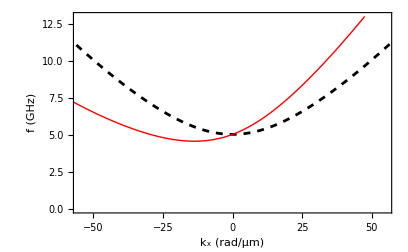

```mathematica
ListPlot[{noDMI,withDMI},Frame->True,FrameLabel->{"k_x (rad/μm)","f (GHz)"},PlotRange->{{-55,55},{0,13}},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->{Directive[Black,Dashed],Directive[Red,Thick]},FrameStyle->Directive[Black,Thick]]
```

Now, the analytic expression by Moon gives:

```mathematica
ωMoon[kx_]:=176/(2. π) (Sqrt[(H[1]+J[1] (2-2 Cos[kx a])) (H[1]+1.05+J[1] (2-2 Cos[kx a]))]+0.0 HDMI[1]/4 Sin[kx a])
```

Which in the long wavelength limit is:

```mathematica
ωMoonApprox[kx_]:=176/(2. π) (Sqrt[(H[1]+J[1] (kx^2 a^2)) (H[1]+1.05+J[1] (kx^2 a^2))]+0.0 HDMI[1] kx a)
```

```mathematica
Table[{kx/10^6,ωMoon[kx]},{kx,-100 10^6,100 10^6,0.5 10^6}]
```

{{-100.,19.7588},{-99.5,19.6457},{-99.,19.533},{-98.5,19.4206},{-98.,19.3085},{-97.5,19.1968},{-97.,19.0854},{-96.5,18.9743},{-96.,18.8635},{-95.5,18.7531},{-95.,18.6431},{-94.5,18.5333},{-94.,18.4239},{-93.5,18.3148},{-93.,18.206},{-92.5,18.0976},{-92.,17.9895},{-91.5,17.8817},{-91.,17.7742},{-90.5,17.6671},{-90.,17.5603},{-89.5,17.4538},{-89.,17.3477},{-88.5,17.2418},{-88.,17.1363},{-87.5,17.0312},{-87.,16.9263},{-86.5,16.8218},{-86.,16.7176},{-85.5,16.6137},{-85.,16.5101},{-84.5,16.4069},{-84.,16.3039},{-83.5,16.2013},{-83.,16.099},{-82.5,15.9971},{-82.,15.8954},{-81.5,15.7941},{-81.,15.6931},{-80.5,15.5924},{-80.,15.4921},{-79.5,15.392},{-79.,15.2923},{-78.5,15.1929},{-78.,15.0938},{-77.5,14.995},{-77.,14.8966},{-76.5,14.7984},{-76.,14.7006},{-75.5,14.6031},{-75.,14.506},{-74.5,14.4091},{-74.,14.3125},{-73.5,14.2163},{-73.,14.1204},{-72.5,14.0248},{-72.,13.9295},{-71.5,13.8346},{-71.,13.74},{-70.5,13.6456},{-70.,13.5516},{-69.5,13.458},{-69.,13.3646},{-68.5,13.2716},{-68.,13.1788},{-67.5,13.0864},{-67.,12.9943},{-66.5,12.9026},{-66.,12.8111},{-65.5,12.72},{-65.,12.6292},{-64.5,12.5388},{-64.,12.4486},{-63.5,12.3588},{-63.,12.2693},{-62.5,12.1801},{-62.,12.0913},{-61.5,12.0027},{-61.,11.9145},{-60.5,11.8267},{-60.,11.7391},{-59.5,11.6519},{-59.,11.5651},{-58.5,11.4785},{-58.,11.3923},{-57.5,11.3064},{-57.,11.2209},{-56.5,11.1357},{-56.,11.0509},{-55.5,10.9663},{-55.,10.8822},{-54.5,10.7983},{-54.,10.7149},{-53.5,10.6317},{-53.,10.5489},{-52.5,10.4665},{-52.,10.3844},{-51.5,10.3027},{-51.,10.2214},{-50.5,10.1404},{-50.,10.0597},{-49.5,9.97946},{-49.,9.89956},{-48.5,9.82003},{-48.,9.74087},{-47.5,9.6621},{-47.,9.5837},{-46.5,9.50569},{-46.,9.42806},{-45.5,9.35083},{-45.,9.27399},{-44.5,9.19755},{-44.,9.12151},{-43.5,9.04588},{-43.,8.97066},{-42.5,8.89585},{-42.,8.82147},{-41.5,8.7475},{-41.,8.67397},{-40.5,8.60087},{-40.,8.52821},{-39.5,8.456},{-39.,8.38424},{-38.5,8.31293},{-38.,8.24209},{-37.5,8.17171},{-37.,8.10181},{-36.5,8.03239},{-36.,7.96346},{-35.5,7.89503},{-35.,7.8271},{-34.5,7.75968},{-34.,7.69278},{-33.5,7.6264},{-33.,7.56056},{-32.5,7.49527},{-32.,7.43052},{-31.5,7.36634},{-31.,7.30273},{-30.5,7.2397},{-30.,7.17727},{-29.5,7.11543},{-29.,7.0542},{-28.5,6.9936},{-28.,6.93363},{-27.5,6.87431},{-27.,6.81564},{-26.5,6.75764},{-26.,6.70033},{-25.5,6.64371},{-25.,6.58779},{-24.5,6.5326},{-24.,6.47814},{-23.5,6.42443},{-23.,6.37149},{-22.5,6.31932},{-22.,6.26794},{-21.5,6.21737},{-21.,6.16763},{-20.5,6.11872},{-20.,6.07067},{-19.5,6.02349},{-19.,5.9772},{-18.5,5.93181},{-18.,5.88735},{-17.5,5.84382},{-17.,5.80125},{-16.5,5.75965},{-16.,5.71904},{-15.5,5.67945},{-15.,5.64088},{-14.5,5.60335},{-14.,5.56689},{-13.5,5.53151},{-13.,5.49722},{-12.5,5.46405},{-12.,5.43202},{-11.5,5.40113},{-11.,5.37141},{-10.5,5.34288},{-10.,5.31555},{-9.5,5.28943},{-9.,5.26455},{-8.5,5.24092},{-8.,5.21855},{-7.5,5.19746},{-7.,5.17766},{-6.5,5.15916},{-6.,5.14199},{-5.5,5.12614},{-5.,5.11163},{-4.5,5.09847},{-4.,5.08667},{-3.5,5.07624},{-3.,5.06718},{-2.5,5.05951},{-2.,5.05322},{-1.5,5.04833},{-1.,5.04483},{-0.5,5.04273},{0.,5.04203},{0.5,5.04273},{1.,5.04483},{1.5,5.04833},{2.,5.05322},{2.5,5.05951},{3.,5.06718},{3.5,5.07624},{4.,5.08667},{4.5,5.09847},{5.,5.11163},{5.5,5.12614},{6.,5.14199},{6.5,5.15916},{7.,5.17766},{7.5,5.19746},{8.,5.21855},{8.5,5.24092},{9.,5.26455},{9.5,5.28943},{10.,5.31555},{10.5,5.34288},{11.,5.37141},{11.5,5.40113},{12.,5.43202},{12.5,5.46405},{13.,5.49722},{13.5,5.53151},{14.,5.56689},{14.5,5.60335},{15.,5.64088},{15.5,5.67945},{16.,5.71904},{16.5,5.75965},{17.,5.80125},{17.5,5.84382},{18.,5.88735},{18.5,5.93181},{19.,5.9772},{19.5,6.02349},{20.,6.07067},{20.5,6.11872},{21.,6.16763},{21.5,6.21737},{22.,6.26794},{22.5,6.31932},{23.,6.37149},{23.5,6.42443},{24.,6.47814},{24.5,6.5326},{25.,6.58779},{25.5,6.64371},{26.,6.70033},{26.5,6.75764},{27.,6.81564},{27.5,6.87431},{28.,6.93363},{28.5,6.9936},{29.,7.0542},{29.5,7.11543},{30.,7.17727},{30.5,7.2397},{31.,7.30273},{31.5,7.36634},{32.,7.43052},{32.5,7.49527},{33.,7.56056},{33.5,7.6264},{34.,7.69278},{34.5,7.75968},{35.,7.8271},{35.5,7.89503},{36.,7.96346},{36.5,8.03239},{37.,8.10181},{37.5,8.17171},{38.,8.24209},{38.5,8.31293},{39.,8.38424},{39.5,8.456},{40.,8.52821},{40.5,8.60087},{41.,8.67397},{41.5,8.7475},{42.,8.82147},{42.5,8.89585},{43.,8.97066},{43.5,9.04588},{44.,9.12151},{44.5,9.19755},{45.,9.27399},{45.5,9.35083},{46.,9.42806},{46.5,9.50569},{47.,9.5837},{47.5,9.6621},{48.,9.74087},{48.5,9.82003},{49.,9.89956},{49.5,9.97946},{50.,10.0597},{50.5,10.1404},{51.,10.2214},{51.5,10.3027},{52.,10.3844},{52.5,10.4665},{53.,10.5489},{53.5,10.6317},{54.,10.7149},{54.5,10.7983},{55.,10.8822},{55.5,10.9663},{56.,11.0509},{56.5,11.1357},{57.,11.2209},{57.5,11.3064},{58.,11.3923},{58.5,11.4785},{59.,11.5651},{59.5,11.6519},{60.,11.7391},{60.5,11.8267},{61.,11.9145},{61.5,12.0027},{62.,12.0913},{62.5,12.1801},{63.,12.2693},{63.5,12.3588},{64.,12.4486},{64.5,12.5388},{65.,12.6292},{65.5,12.72},{66.,12.8111},{66.5,12.9026},{67.,12.9943},{67.5,13.0864},{68.,13.1788},{68.5,13.2716},{69.,13.3646},{69.5,13.458},{70.,13.5516},{70.5,13.6456},{71.,13.74},{71.5,13.8346},{72.,13.9295},{72.5,14.0248},{73.,14.1204},{73.5,14.2163},{74.,14.3125},{74.5,14.4091},{75.,14.506},{75.5,14.6031},{76.,14.7006},{76.5,14.7984},{77.,14.8966},{77.5,14.995},{78.,15.0938},{78.5,15.1929},{79.,15.2923},{79.5,15.392},{80.,15.4921},{80.5,15.5924},{81.,15.6931},{81.5,15.7941},{82.,15.8954},{82.5,15.9971},{83.,16.099},{83.5,16.2013},{84.,16.3039},{84.5,16.4069},{85.,16.5101},{85.5,16.6137},{86.,16.7176},{86.5,16.8218},{87.,16.9263},{87.5,17.0312},{88.,17.1363},{88.5,17.2418},{89.,17.3477},{89.5,17.4538},{90.,17.5603},{90.5,17.6671},{91.,17.7742},{91.5,17.8817},{92.,17.9895},{92.5,18.0976},{93.,18.206},{93.5,18.3148},{94.,18.4239},{94.5,18.5333},{95.,18.6431},{95.5,18.7531},{96.,18.8635},{96.5,18.9743},{97.,19.0854},{97.5,19.1968},{98.,19.3085},{98.5,19.4206},{99.,19.533},{99.5,19.6457},{100.,19.7588}}

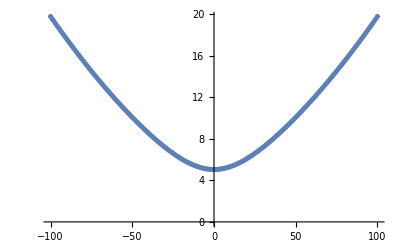

```mathematica
ListPlot[Table[{kx/10^6,ωMoon[kx]},{kx,-100 10^6,100 10^6,1 10^6}]]
```

```mathematica
withDMIanalytic={{-100.,12.71950539006153},{-99.5,12.641623018429604},{-99.,12.564074983182062},{-98.5,12.48686078161367},{-98.,12.40997991401042},{-97.5,12.333431883820158},{-97.,12.257216197840803},{-96.5,12.181332366397404},{-96.,12.105779903532953},{-95.5,12.030558327217364},{-95.,11.955667159533192},{-94.5,11.881105926896511},{-94.,11.806874160267302},{-93.5,11.732971395362004},{-93.,11.65939717290199},{-92.5,11.586151038822633},{-92.,11.51323254453133},{-91.5,11.440641247151694},{-91.,11.368376709775102},{-90.5,11.296438501736798},{-90.,11.224826198870161},{-89.5,11.153539383798714},{-89.,11.082577646206616},{-88.5,11.011940583164867},{-88.,10.941627799410588},{-87.5,10.871638907661039},{-87.,10.801973528963048},{-86.5,10.732631292991556},{-86.,10.663611838418714},{-85.5,10.594914813258608},{-85.,10.526539875222461},{-84.5,10.458486692106616},{-84.,10.390754942178688},{-83.5,10.323344314562146},{-83.,10.256254509659145},{-82.5,10.189485239568215},{-82.,10.123036228510063},{-81.5,10.05690721329326},{-81.,9.991097943766771},{-80.5,9.92560818328635},{-80.,9.86043770921771},{-79.5,9.795586313436713},{-79.,9.731053802844754},{-78.5,9.666839999918162},{-78.,9.602944743237536},{-77.5,9.539367888074821},{-77.,9.476109306984265},{-76.5,9.413168890379085},{-76.,9.350546547186326},{-75.5,9.28824220546564},{-75.,9.226255813089338},{-74.5,9.164587338396307},{-74.,9.103236770936842},{-73.5,9.042204122150428},{-73.,8.981489426154814},{-72.5,8.921092740483083},{-72.,8.861014146891552},{-71.5,8.80125375218775},{-71.,8.741811689055229},{-70.5,8.682688116937916},{-70.,8.62388322292766},{-69.5,8.565397222689203},{-69.,8.50723036143355},{-68.5,8.44938291487258},{-68.,8.39185519024798},{-67.5,8.3346475273873},{-67.,8.277760299763322},{-66.5,8.221193915616581},{-66.,8.164948819108059},{-65.5,8.109025491492973},{-65.,8.053424452346635},{-64.5,7.998146260818663},{-64.,7.943191516947003},{-63.5,7.88856086297748},{-63.,7.834254984760865},{-62.5,7.780274613168082},{-62.,7.726620525560352},{-61.5,7.67329354733157},{-61.,7.620294553420866},{-60.5,7.567624469982943},{-60.,7.515284276005506},{-59.5,7.46327500506218},{-59.,7.411597747056655},{-58.5,7.360253650064221},{-58.,7.309243922193456},{-57.5,7.25856983357071},{-57.,7.208232718289128},{-56.5,7.15823397651084},{-56.,7.1085750765852636},{-55.5,7.05925755724408},{-55.,7.01028302985854},{-54.5,6.96165318077739},{-54.,6.913369773731035},{-53.5,6.865434652320419},{-53.,6.817849742531054},{-52.5,6.77061705541941},{-52.,6.723738689777998},{-51.5,6.677216834943184},{-51.,6.63105377367523},{-50.5,6.585251885106242},{-50.,6.539813647792129},{-49.5,6.494741642853545},{-49.,6.450038557184096},{-48.5,6.405707186779801},{-48.,6.361750440162896},{-47.5,6.318171341865741},{-47.,6.27497303604696},{-46.5,6.232158790200272},{-46.,6.18973199894486},{-45.5,6.147696187928131},{-45.,6.1060550178422055},{-44.5,6.06481228853058},{-44.,6.023971943178609},{-43.5,5.983538072637297},{-43.,5.943514919837393},{-42.5,5.903906884311826},{-42.,5.864718526800366},{-41.5,5.8259545739728775},{-41.,5.787619923237989},{-40.5,5.749719647673282},{-40.,5.712259001003455},{-39.5,5.675243422699912},{-39.,5.638678543192469},{-38.5,5.602570189062875},{-38.,5.566924388458172},{-37.5,5.531747376420094},{-37.,5.497045600401392},{-36.5,5.462825725747415},{-36.,5.42909464126687},{-35.5,5.395859464827565},{-35.,5.363127548957484},{-34.5,5.330906486443889},{-34.,5.2992041159572585},{-33.5,5.2680285276206735},{-33.,5.237388068540573},{-32.5,5.207291348271344},{-32.,5.177747244183994},{-31.5,5.148764906735824},{-31.,5.120353764600168},{-30.5,5.092523529604668},{-30.,5.065284201482674},{-29.5,5.038646072404177},{-29.,5.0126197312196545},{-28.5,4.987216067368687},{-28.,4.962446274471053},{-27.5,4.938321853502306},{-27.,4.914854615527864},{-26.5,4.892056683912812},{-26.,4.869940495998999},{-25.5,4.848518804152851},{-25.,4.827804676162433},{-24.5,4.807811494872624},{-24.,4.788552957015071},{-23.5,4.770043071180068},{-23.,4.752296154843007},{-22.5,4.7353268303467635},{-22.,4.719150019805076},{-21.5,4.703780938850909},{-21.,4.689235089110458},{-20.5,4.675528249357804},{-20.,4.662676465247245},{-19.5,4.650696037615339},{-19.,4.639603509167413},{-18.5,4.62941564957075},{-18.,4.620149438853266},{-17.5,4.611822049000926},{-17.,4.604450823820989},{-16.5,4.598053256873332},{-16.,4.592646967553901},{-15.5,4.588249675185217},{-15.,4.5848791711947054},{-14.5,4.582553289396908},{-14.,4.581289874216619},{-13.5,4.581106747089477},{-13.,4.582021670985331},{-12.5,4.584052313070525},{-12.,4.587216205704176},{-11.5,4.591530705799173},{-11.,4.597012952702398},{-10.5,4.603679824695347},{-10.,4.611547894381945},{-9.5,4.62063338305286},{-9.,4.630952114338334},{-8.5,4.642519467261459},{-8.,4.6553503291237615},{-7.5,4.6694590483246285},{-7.,4.684859387523278},{-6.5,4.701564477400869},{-6.,4.719586771339473},{-5.5,4.738938001392065},{-5.,4.759629135762818},{-4.5,4.781670338244916},{-4.,4.805070929920827},{-3.5,4.8298393533201915},{-3.,4.855983139477538},{-2.5,4.883508878185635},{-2.,4.91242219151649},{-1.5,4.942727711088891},{-1.,4.974429059109371},{-0.5,5.007528833512974},{0.,5.042028597151244},{0.5,5.077928871350958},{1.,5.115229133702868},{1.5,5.153927820272959},{2.,5.194022332043715},{2.5,5.235509045726134},{3.,5.278383328618957},{3.5,5.322639557567704},{4.,5.368271141697137},{4.5,5.415270548890258},{5.,5.4636293355349554},{5.5,5.51333817946629},{6.,5.564386915808609},{6.5,5.616764575275269},{7.,5.670459424730825},{7.5,5.725459009710735},{8.,5.781750198451375},{8.5,5.839319227211053},{9.,5.898151746507916},{9.5,5.958232867957968},{10.,6.0195472114556505},{10.5,6.082078952288253},{11.,6.145811868082638},{11.5,6.2107293851524155},{12.,6.276814624133622},{12.5,6.344050444596909},{13.,6.412419488546922},{13.5,6.481904222542076},{14.,6.552486978333569},{14.5,6.624149991869079},{15.,6.696875440630507},{15.5,6.770645479110595},{16.,6.845442272412337},{16.5,6.921248028025846},{17.,6.998045025546139},{17.5,7.075815644494806},{18.,7.154542390229512},{18.5,7.234207917860534},{19.,7.314795054319451},{19.5,7.396286818495885},{20.,7.478666439640097},{20.5,7.561917373964296},{21.,7.6460233195494745},{21.5,7.730968229658873},{22.,7.816736324435957},{22.5,7.903312101172073},{23.,7.990680343151805},{23.5,8.078826127178958},{24.,8.167734829828204},{24.5,8.2573921325417},{25.,8.347784025646703},{25.5,8.438896811329109},{26.,8.530717105661594},{26.5,8.623231839773645},{27.,8.716428260216382},{27.5,8.810293928565518},{28.,8.90481672037351},{28.5,8.999984823492506},{29.,9.095786735864502},{29.5,9.192211262787275},{30.,9.289247513738808},{30.5,9.386884898786175},{31.,9.485113124676948},{31.5,9.583922190595338},{32.,9.683302383631265},{32.5,9.783244274028956},{33.,9.883738710248673},{33.5,9.984776813836973},{34.,10.086349974157038},{34.5,10.188449843019992},{35.,10.291068329220325},{35.5,10.394197593005128},{36.,10.497830040504704},{36.5,10.601958318108647},{37.,10.70657530686672},{37.5,10.811674116887788},{38.,10.917248081744079},{38.5,11.023290752900419},{39.,11.12979589423265},{39.5,11.236757476511313},{40.,11.34416967207223},{40.5,11.452026849403175},{41.,11.560323567950325},{41.5,11.669054572906566},{42.,11.778214790111901},{42.5,11.88779932107529},{43.,11.997803438044455},{43.5,12.108222579197214},{44.,12.21905234391824},{44.5,12.33028848819436},{45.,12.441926920092179},{45.5,12.553963695343926},{46.,12.666395013023713},{46.5,12.77921721135701},{47.,12.892426763614012},{47.5,13.00602027409314},{48.,13.119994474218275},{48.5,13.234346218748403},{49.,13.349072482068769},{49.5,13.464170354574737},{50.,13.57963703918791},{50.5,13.695469847932284},{51.,13.811666198604822},{51.5,13.92822361156723},{52.,14.045139706605019},{52.5,14.162412199875545},{53.,14.28003890096006},{53.5,14.398017709983675},{54.,14.516346614807544},{54.5,14.63502368836378},{55.,14.754047085969068},{55.5,14.873415042810631},{56.,14.993125871457346},{56.5,15.11317795945561},{57.,15.233569766991359},{57.5,15.354299824632822},{58.,15.475366731135507},{58.5,15.596769151323908},{59.,15.718505813989314},{59.5,15.840575509940791},{60.,15.962977090020694},{60.5,16.08570946324299},{61.,16.208771594951692},{61.5,16.332162505076756},{62.,16.45588126638113},{62.5,16.57992700284333},{63.,16.70429888798714},{63.5,16.82899614336898},{64.,16.954018037035596},{64.5,17.079363882053883},{65.,17.205033035095678},{65.5,17.331024895040706},{66.,17.45733890165702},{66.5,17.583974534286984},{67.,17.710931310593047},{67.5,17.838208785331908},{68.,17.965806549180716},{68.5,18.09372422758437},{69.,18.221961479633002},{69.5,18.350517997002605},{70.,18.479393502899004},{70.5,18.608587751028875},{71.,18.738100524645166},{71.5,18.86793163557373},{72.,18.998080923288335},{72.5,19.128548254023134},{73.,19.259333519888294},{73.5,19.39043663804521},{74.,19.521857549878497},{74.5,19.653596220188124},{75.,19.78565263645232},{75.5,19.918026808038494},{76.,20.050718765525495},{76.5,20.183728559958716},{77.,20.317056262196232},{77.5,20.450701962228724},{78.,20.584665768560704},{78.5,20.71894780755565},{79.,20.853548222859352},{79.5,20.98846717480895},{80.,21.123704839845853},{80.5,21.2592614099864},{81.,21.395137092272474},{81.5,21.531332108256112},{82.,21.667846693499314},{82.5,21.80468109707085},{83.,21.941835581079914},{83.5,22.079310420223557},{84.,22.217105901321005},{84.5,22.355222322887865},{85.,22.493659994718445},{85.5,22.63241923746288},{86.,22.771500382242607},{86.5,22.910903770264177},{87.,23.05062975243128},{87.5,23.190678688989543},{88.,23.33105094918181},{88.5,23.471746910879034},{89.,23.61276696028175},{89.5,23.75411149157062},{90.,23.895780906592446},{90.5,24.037775614580863},{91.,24.18009603183014},{91.5,24.322742581424716},{92.,24.465715692947146},{92.5,24.609015802223862},{93.,24.752643351049066},{93.5,24.896598786933172},{94.,25.040882562858627},{94.5,25.185495137021878},{95.,25.330436972624312},{95.5,25.47570853762378},{96.,25.62131030452204},{96.5,25.76724275015436},{97.,25.91350635546867},{97.5,26.06010160533982},{98.,26.20702898836061},{98.5,26.354288996650954},{99.,26.501882125680865},{99.5,26.649808874082204},{100.,26.798069743478063}};
```

```mathematica
noDMIanalytic={{-100.,19.758787566769794},{-99.5,19.645715946255905},{-99.,19.532978554431462},{-98.5,19.42057488913231},{-98.,19.308504451185513},{-97.5,19.19676674457999},{-97.,19.085361276654737},{-96.5,18.974287558275883},{-96.,18.863545104027498},{-95.5,18.753133432420572},{-95.,18.643052066078756},{-94.5,18.533300531959195},{-94.,18.423878361562963},{-93.5,18.314785091147588},{-93.,18.206020261975528},{-92.5,18.09758342052325},{-92.,17.98947411873924},{-91.5,17.881691914288208},{-91.,17.774236370802623},{-90.5,17.66710705815883},{-90.,17.560303552731302},{-89.5,17.453825437684667},{-89.,17.347672303244185},{-88.5,17.24184374702195},{-88.,17.1363393742962},{-87.5,17.03115879832529},{-87.,16.926301640697165},{-86.5,16.821767531627867},{-86.,16.717556110330662},{-85.5,16.613667025360744},{-85.,16.51009993497045},{-84.5,16.40685450749724},{-84.,16.303930421749847},{-83.5,16.20132736739285},{-83.,16.09904504536953},{-82.5,15.997083168319532},{-82.,15.895441461004689},{-81.5,15.794119660774685},{-81.,15.693117518019623},{-80.5,15.592434796636374},{-80.,15.492071274531781},{-79.5,15.392026744122832},{-79.,15.292301012852054},{-78.5,15.192893903736907},{-78.,15.09380525589912},{-77.5,14.995034925151772},{-77.,14.89658278459025},{-76.5,14.7984487251689},{-76.,14.70063265635591},{-75.5,14.603134506752067},{-75.,14.505954224770829},{-74.5,14.409091779292215},{-74.,14.31254716040767},{-73.5,14.21632038009782},{-73.,14.120411473021555},{-72.5,14.024820497253108},{-72.,13.929547535089943},{-71.5,13.834592693880738},{-71.,13.739956106850197},{-70.5,13.645637933983396},{-70.,13.551638362913332},{-69.5,13.457957609845906},{-69.,13.364595920533274},{-68.5,13.271553571228475},{-68.,13.178830869714348},{-67.5,13.086428156359604},{-67.,12.994345805178185},{-66.5,12.902584224951783},{-66.,12.81114386038254},{-65.5,12.72002519326684},{-65.,12.629228743721157},{-64.5,12.538755071436272},{-64.,12.4486047769913},{-63.5,12.35877850317323},{-63.,12.269276936374002},{-62.5,12.180100808005706},{-62.,12.09125089597074},{-61.5,12.002728026204164},{-61.,11.914533074186279},{-60.5,11.826666966612965},{-60.,11.7391306830131},{-59.5,11.651925257501485},{-59.,11.565051780522984},{-58.5,11.478511400694066},{-58.,11.39230532666448},{-57.5,11.306434829101766},{-57.,11.220901242640243},{-56.5,11.135705967983226},{-56.,11.050850474021304},{-55.5,10.966336300027356},{-55.,10.882165057913804},{-54.5,10.798338434570585},{-54.,10.71485819426929},{-53.5,10.631726181152047},{-53.,10.548944321745557},{-52.5,10.466514627647477},{-52.,10.38443919819151},{-51.5,10.302720223255207},{-51.,10.221359986140026},{-50.5,10.140360866519263},{-50.,10.059725343490019},{-49.5,9.97945599871414},{-49.,9.899555519626432},{-48.5,9.820026702764102},{-48.,9.740872457190585},{-47.5,9.66209580797944},{-47.,9.583699899830487},{-46.5,9.505688000778642},{-46.,9.428063505984285},{-45.5,9.350829941636029},{-45.,9.273990968967192},{-44.5,9.19755038836247},{-44.,9.121512143548424},{-43.5,9.045880325917256},{-43.,8.970659178940924},{-42.5,8.895853102693557},{-42.,8.821466658456133},{-41.5,8.747504573439722},{-41.,8.673971745594157},{-40.5,8.600873248538228},{-40.,8.528214336537843},{-39.5,8.456000449605613},{-39.,8.38423721871256},{-38.5,8.312930470981646},{-38.,8.242086235101125},{-37.5,8.171710746653941},{-37.,8.101810453634057},{-36.5,8.03239202192803},{-36.,7.963462340885788},{-35.5,7.895028528916346},{-35.,7.827097939088905},{-34.5,7.759678164731941},{-34.,7.692777045057148},{-33.5,7.626402670728823},{-33.,7.560563389394623},{-32.5,7.49526781115015},{-32.,7.430524813907629},{-31.5,7.366343548665581},{-31.,7.302733444638558},{-30.5,7.239704214195422},{-30.,7.177265857610741},{-29.5,7.115428667595726},{-29.,7.0542032335420775},{-28.5,6.993600445430596},{-28.,6.933631497422282},{-27.5,6.8743078910339115},{-27.,6.815641437872124},{-26.5,6.757644261843228},{-26.,6.700328800830296},{-25.5,6.64370780774098},{-25.,6.587794350904568},{-24.5,6.532601813707162},{-24.,6.478143893421638},{-23.5,6.424434599179512},{-23.,6.371488248997406},{-22.5,6.319319465759418},{-22.,6.267943172120517},{-21.5,6.217374584254891},{-21.,6.167629204329966},{-20.5,6.11872281166105},{-20.,6.070671452443671},{-19.5,6.023491428055612},{-19.,5.977199281743432},{-18.5,5.931811783715641},{-18.,5.887345914541389},{-17.5,5.843818846747866},{-17.,5.801247924683564},{-16.5,5.759650642449588},{-16.,5.719044619983119},{-15.5,5.679447577147906},{-15.,5.640877305912606},{-14.5,5.603351640632994},{-14.,5.566888426275094},{-13.5,5.531505484815776},{-13.,5.497220579766127},{-12.5,5.464051378833717},{-12.,5.432015414918899},{-11.5,5.401130045475795},{-11.,5.3714124103925185},{-10.5,5.3428793884917996},{-10.,5.315547552918797},{-9.5,5.289433125505414},{-9.,5.264551930423125},{-8.5,5.240919347236256},{-8.,5.218550263787568},{-7.5,5.197459029017682},{-7.,5.177659406127051},{-6.5,5.15916452633807},{-6.,5.141986843574041},{-5.5,5.126138090429178},{-5.,5.111629235648887},{-4.5,5.098470443567587},{-4.,5.086671035808982},{-3.5,5.076239455443948},{-3.,5.067183234048247},{-2.5,5.059508961955885},{-2.,5.053222261780102},{-1.5,5.048327765680925},{-1.,5.0448290964061195},{-0.5,5.042728852431965},{0.,5.042028597151244},{0.5,5.042728852431965},{1.,5.0448290964061195},{1.5,5.048327765680925},{2.,5.053222261780102},{2.5,5.059508961955885},{3.,5.067183234048247},{3.5,5.076239455443948},{4.,5.086671035808982},{4.5,5.098470443567587},{5.,5.111629235648887},{5.5,5.126138090429178},{6.,5.141986843574041},{6.5,5.15916452633807},{7.,5.177659406127051},{7.5,5.197459029017682},{8.,5.218550263787568},{8.5,5.240919347236256},{9.,5.264551930423125},{9.5,5.289433125505414},{10.,5.315547552918797},{10.5,5.3428793884917996},{11.,5.3714124103925185},{11.5,5.401130045475795},{12.,5.432015414918899},{12.5,5.464051378833717},{13.,5.497220579766127},{13.5,5.531505484815776},{14.,5.566888426275094},{14.5,5.603351640632994},{15.,5.640877305912606},{15.5,5.679447577147906},{16.,5.719044619983119},{16.5,5.759650642449588},{17.,5.801247924683564},{17.5,5.843818846747866},{18.,5.887345914541389},{18.5,5.931811783715641},{19.,5.977199281743432},{19.5,6.023491428055612},{20.,6.070671452443671},{20.5,6.11872281166105},{21.,6.167629204329966},{21.5,6.217374584254891},{22.,6.267943172120517},{22.5,6.319319465759418},{23.,6.371488248997406},{23.5,6.424434599179512},{24.,6.478143893421638},{24.5,6.532601813707162},{25.,6.587794350904568},{25.5,6.64370780774098},{26.,6.700328800830296},{26.5,6.757644261843228},{27.,6.815641437872124},{27.5,6.8743078910339115},{28.,6.933631497422282},{28.5,6.993600445430596},{29.,7.0542032335420775},{29.5,7.115428667595726},{30.,7.177265857610741},{30.5,7.239704214195422},{31.,7.302733444638558},{31.5,7.366343548665581},{32.,7.430524813907629},{32.5,7.49526781115015},{33.,7.560563389394623},{33.5,7.626402670728823},{34.,7.692777045057148},{34.5,7.759678164731941},{35.,7.827097939088905},{35.5,7.895028528916346},{36.,7.963462340885788},{36.5,8.03239202192803},{37.,8.101810453634057},{37.5,8.171710746653941},{38.,8.242086235101125},{38.5,8.312930470981646},{39.,8.38423721871256},{39.5,8.456000449605613},{40.,8.528214336537843},{40.5,8.600873248538228},{41.,8.673971745594157},{41.5,8.747504573439722},{42.,8.821466658456133},{42.5,8.895853102693557},{43.,8.970659178940924},{43.5,9.045880325917256},{44.,9.121512143548424},{44.5,9.19755038836247},{45.,9.273990968967192},{45.5,9.350829941636029},{46.,9.428063505984285},{46.5,9.505688000778642},{47.,9.583699899830487},{47.5,9.66209580797944},{48.,9.740872457190585},{48.5,9.820026702764102},{49.,9.899555519626432},{49.5,9.97945599871414},{50.,10.059725343490019},{50.5,10.140360866519263},{51.,10.221359986140026},{51.5,10.302720223255207},{52.,10.38443919819151},{52.5,10.466514627647477},{53.,10.548944321745557},{53.5,10.631726181152047},{54.,10.71485819426929},{54.5,10.798338434570585},{55.,10.882165057913804},{55.5,10.966336300027356},{56.,11.050850474021304},{56.5,11.135705967983226},{57.,11.220901242640243},{57.5,11.306434829101766},{58.,11.39230532666448},{58.5,11.478511400694066},{59.,11.565051780522984},{59.5,11.651925257501485},{60.,11.7391306830131},{60.5,11.826666966612965},{61.,11.914533074186279},{61.5,12.002728026204164},{62.,12.09125089597074},{62.5,12.180100808005706},{63.,12.269276936374002},{63.5,12.35877850317323},{64.,12.4486047769913},{64.5,12.538755071436272},{65.,12.629228743721157},{65.5,12.72002519326684},{66.,12.81114386038254},{66.5,12.902584224951783},{67.,12.994345805178185},{67.5,13.086428156359604},{68.,13.178830869714348},{68.5,13.271553571228475},{69.,13.364595920533274},{69.5,13.457957609845906},{70.,13.551638362913332},{70.5,13.645637933983396},{71.,13.739956106850197},{71.5,13.834592693880738},{72.,13.929547535089943},{72.5,14.024820497253108},{73.,14.120411473021555},{73.5,14.21632038009782},{74.,14.31254716040767},{74.5,14.409091779292215},{75.,14.505954224770829},{75.5,14.603134506752067},{76.,14.70063265635591},{76.5,14.7984487251689},{77.,14.89658278459025},{77.5,14.995034925151772},{78.,15.09380525589912},{78.5,15.192893903736907},{79.,15.292301012852054},{79.5,15.392026744122832},{80.,15.492071274531781},{80.5,15.592434796636374},{81.,15.693117518019623},{81.5,15.794119660774685},{82.,15.895441461004689},{82.5,15.997083168319532},{83.,16.09904504536953},{83.5,16.20132736739285},{84.,16.303930421749847},{84.5,16.40685450749724},{85.,16.51009993497045},{85.5,16.613667025360744},{86.,16.717556110330662},{86.5,16.821767531627867},{87.,16.926301640697165},{87.5,17.03115879832529},{88.,17.1363393742962},{88.5,17.24184374702195},{89.,17.347672303244185},{89.5,17.453825437684667},{90.,17.560303552731302},{90.5,17.66710705815883},{91.,17.774236370802623},{91.5,17.881691914288208},{92.,17.98947411873924},{92.5,18.09758342052325},{93.,18.206020261975528},{93.5,18.314785091147588},{94.,18.423878361562963},{94.5,18.533300531959195},{95.,18.643052066078756},{95.5,18.753133432420572},{96.,18.863545104027498},{96.5,18.974287558275883},{97.,19.085361276654737},{97.5,19.19676674457999},{98.,19.308504451185513},{98.5,19.42057488913231},{99.,19.532978554431462},{99.5,19.645715946255905},{100.,19.758787566769794}};
```

Now putting it all together (analytic by Moon as lines, and numerical results here as dots):

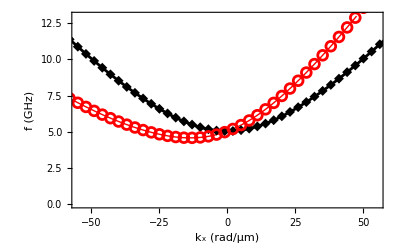

```mathematica
fig2=ListPlot[{noDMIanalytic,withDMIanalytic,Table[noDMI[[i]],{i,1,Length[noDMI],3}],Table[withDMI[[i]],{i,1,Length[noDMI],3}]},Frame->True,FrameLabel->{"k_x (rad/μm)","f (GHz)"},PlotRange->{{-55,55},{0,13}},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->{True,True,False,False},PlotStyle->{Directive[Black,Medium],Directive[Red,Thick],Directive[Black,PointSize[0.019]],Directive[Red,PointSize[0.019]]},FrameStyle->Directive[Black,Thick],PlotMarkers->{None,None,Automatic,Graphics[{Red,Thick,Circle[]},ImageSize->10]}]
```

```mathematica
Export["/Users/karen/Desktop/UON stuff/Students/Ellen/Spin waves DMI/Fig2_dispersion.jpg",fig2,ImageResolution->1000]
```

/Users/karen/Desktop/UON stuff/Students/Ellen/Spin waves DMI/Fig2_dispersion.jpg

A great match!

Export to ppt to add labels.






Looking at the percentage difference:

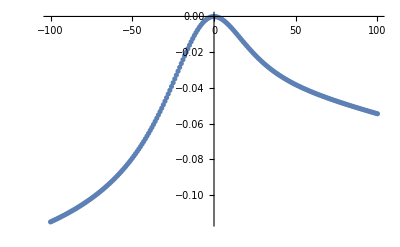

```mathematica
ListPlot[Table[{withDMI[[i]][[1]],(withDMI[[i]][[2]]-withDMIanalytic[[2 i-1]][[2]])/(withDMI[[i]][[2]]) 100},{i,1,Length[withDMI]}]]
```

There is less than 0.15% difference between the analytic and numeric result, as discussed in the article, due to relaxation of the uniform mode assumption.